# Too Much Time and Too Little Time Linked to Lower Subjective Well Being

If R^2 is low, then you can suspect mean model error.

-Graphics-

Use the coefficients.  
What does /. mean?
It means replace values.

Note that Wolfram Engine is stringent to *

Claim is made for coefficient to be robustly is zero.

```mathematica
?/.
```

```mathematica
f=a*x+b*x^2+c/.{a->.027,b->-.004,c->7.134}
```

7.134+0.027 x-0.004 x^2

Plot the trend line for the plot.

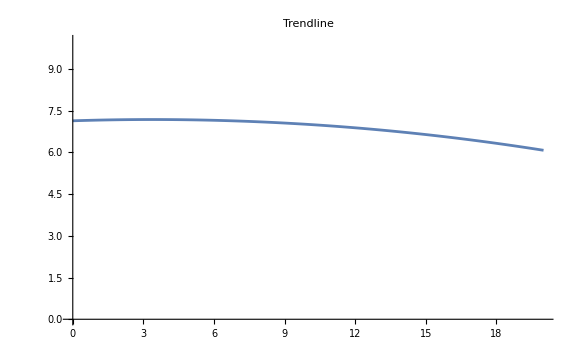

```mathematica
Plot[f,{x,0,20},PlotRange->{0,10},PlotLabel->"Trendline",ImageSize->Large]
```

Replicate the table, how is the table replicated?

```mathematica
X=Table[i,{i,1,24,1/2}]
```

{1,3/2,2,5/2,3,7/2,4,9/2,5,11/2,6,13/2,7,15/2,8,17/2,9,19/2,10,21/2,11,23/2,12,25/2,13,27/2,14,29/2,15,31/2,16,33/2,17,35/2,18,37/2,19,39/2,20,41/2,21,43/2,22,45/2,23,47/2,24}

Nassim Taleb had the following.
He had the figure of the number of observations to hours.
This was obtained from another version of the paper by Adam Grant.

```mathematica
Y={838,828,1181,1136,1306,1167,1222,1113,1073,1006,1002,953,848,779,729,688,585,546,514,447,412,350,319,246,227,204,161,120,84,63,41,21,35,15,21,6,8,2,9,2,1,5,1,1,1,1,1}
```

{838,828,1181,1136,1306,1167,1222,1113,1073,1006,1002,953,848,779,729,688,585,546,514,447,412,350,319,246,227,204,161,120,84,63,41,21,35,15,21,6,8,2,9,2,1,5,1,1,1,1,1}

```mathematica
ta=Table[Table[X[[i]],{Y[[i]]}],{i,1,Length[X]}]//Flatten;
```

Makes the distribution into an empirical distribution.

```mathematica
dist=EmpiricalDistribution[ta]
```

DataDistribution[…]

From a power law discussion, the square of a variable has half the tail exponent.

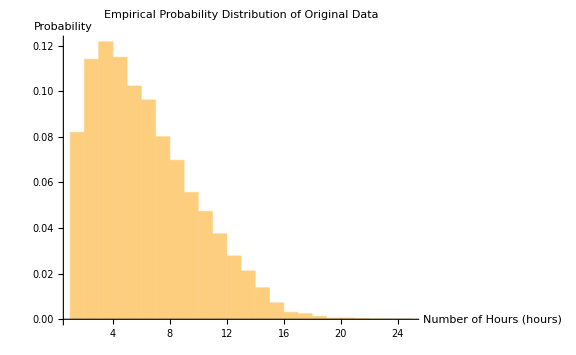

```mathematica
Histogram[ta,30,Probability,PlotLabel->"Empirical Probability Distribution of Original Data",AxesLabel->{"Number of Hours (hours)","Probability"},ImageSize->Large]
```

We take the square of the number of hours given the claims of a quadratic fit. The squared variable has half the tail exponent.

```mathematica
tasquare=Table[Table[X[[i]]^2,{Y[[i]]}],{i,1,Length[X]}]//Flatten;
```

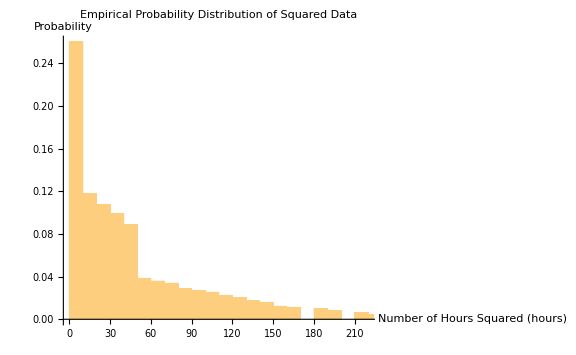

```mathematica
Histogram[tasquare,50,Probability,PlotLabel->"Empirical Probability Distribution of Squared Data",AxesLabel->{"Number of Hours Squared (hours)","Probability"},ImageSize->Large]
```

This is the key step in replicating the paper. Take the smooth kernel distribution. It makes the distribution of the bins smoother.

```mathematica
dist2=SmoothKernelDistribution[ta];
```

Apply N to all these values which makes them real and not fractions.

```mathematica
{Mean[dist2],Kurtosis[dist2],Skewness[dist2]}//N
```

{6.02567,3.17826,0.750064}

```mathematica
{Skewness[ta],Skewness[dist2]}//N
```

{0.767495,0.750064}

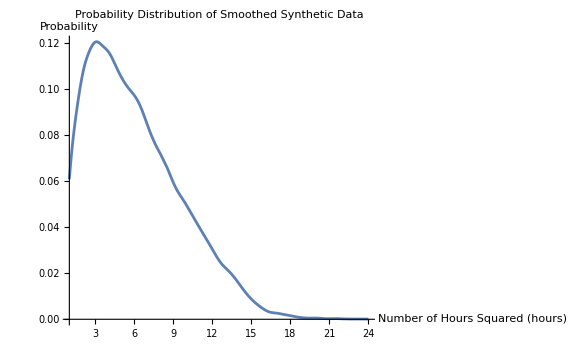

```mathematica
Plot[PDF[dist2,x],{x,1,24},PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Number of Hours Squared (hours)","Probability"},ImageSize->Large]
```

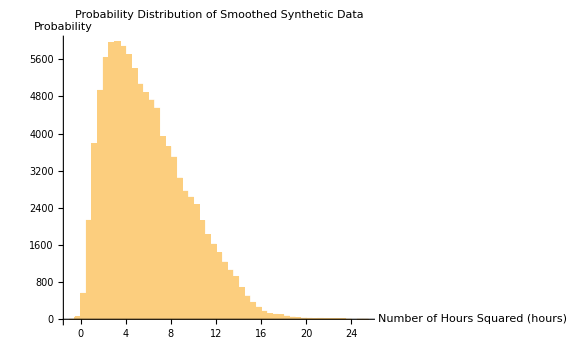

```mathematica
Histogram[RandomVariate[dist2,10^5],50,PlotLabel->"Probability Distribution of Smoothed Synthetic Data",AxesLabel->{"Number of Hours Squared (hours)","Probability"},ImageSize->Large]
```

### Testing with No Noise

```mathematica
f=a*x+b*x^2+c/.{a->.044,b->-.003,c->3.180};
f=a*x+b*x^2+c/.{a->.027,b->-.004,c->7.134};
```

Apply the regression line to the original function.

```mathematica
f1=f/.x->ta;
```

```mathematica
reg=Transpose[{ta,f1}];
```

```mathematica
lm=LinearModelFit[reg,{1,x,x^2},x];
```

Recall the table above was to get this linear regression fit of R^2=1 given the coefficients.

```mathematica
lm
```

FittedModel[7.134+0.027 x-0.004 x^2]

```mathematica
lm["RSquared"]
```

1.

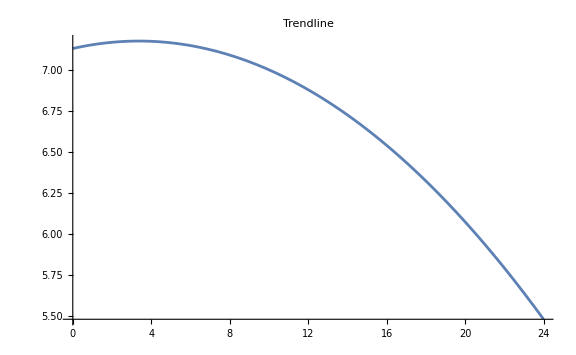

```mathematica
Plot[lm[x],{x,0,24},PlotLabel->"Trendline",ImageSize->Large]
```

Obtain the length of f1 based on the length of samples in ta.

```mathematica
f1//Length
```

20318

Apply some Gaussian noise to the function. Then perform the transpose to make it suitable for regression again.

```mathematica
reg1[sigma_]:=Transpose[{ta,f1+RandomVariate[NormalDistribution[0,sigma],Length[f1]]}]
```

Then, apply a linear model fit with the model. Check the R^2 as usual, run about the model 10^4 times so as to get a distribution of possible R^2 values. This is the Monte Carlo simulation for possible R^2 and eats up a lot of time.

```mathematica
res=Table[lm=LinearModelFit[reg1[.75],{1,x,x^2},x];lm["RSquared"],{z,1,10^3}];
```

Get the assumed R^2 distribution and parameters. It is almost Gaussian.

```mathematica
{Mean[res],StandardDeviation[res],Skewness[res],Kurtosis[res]}
```

{0.029769,0.00234075,0.108276,2.88982}

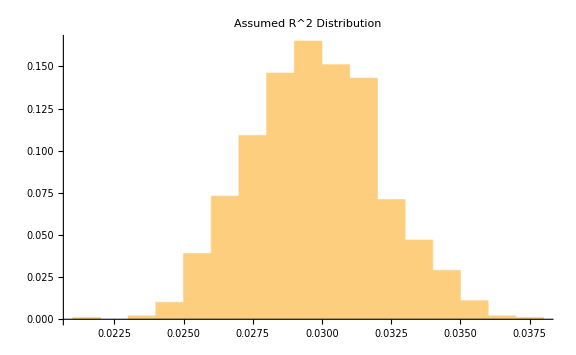

```mathematica
pl0=Histogram[res,Automatic,"Probability",PlotLabel->"Assumed R^2 Distribution",ImageSize->Large]
```

Replicate the graph that slopes down because of the lack of observations. This is why their slope is quadratic.

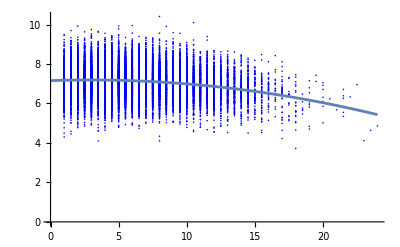

```mathematica
Show[ListPlot[reg1[.75],PlotStyle->Blue],Plot[lm[x],{x,0,24}]]
```

### Replicating Their Quadratic Term

Apply the same technique, tabulate the values of the second coefficient, run the Monte Carlo simulation 10^4 times.

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[.75],{1,x,x^2},x];lm2[x][[3]][[1]],{z,1,10^3}]
```

{-0.00406761,-0.00402669,-0.00386268,-0.00380451,-0.0043143,-0.00396163,-0.00329766,-0.00386285,-0.00416747,-0.00385125,-0.00374899,-0.0037796,-0.00330206,-0.0038791,-0.00344312,-0.0042753,-0.00400476,-0.00415724,-0.00380094,-0.00394211,-0.00409844,-0.00425373,-0.003671,-0.0048174,-0.00396366,-0.00500214,-0.00364142,-0.0039527,-0.00410472,-0.00367174,-0.00399032,-0.00400877,-0.00403364,-0.00396003,-0.00380861,-0.00460854,-0.00446961,-0.00417206,-0.00384988,-0.00359684,-0.00433426,-0.00395273,-0.00382181,-0.00420609,-0.00397231,-0.00410071,-0.00444579,-0.00419258,-0.00374546,-0.00425557,-0.00365531,-0.00402091,-0.00406163,-0.00409453,-0.00375851,-0.00411091,-0.00348278,-0.00450176,-0.00418606,-0.00391248,-0.00382721,-0.00367916,-0.0035775,-0.00375888,-0.00401766,-0.00444742,-0.00419697,-0.00407535,-0.00370134,-0.00409241,-0.00365907,-0.00392729,-0.00417562,-0.00397673,-0.00391494,-0.00391157,-0.00378292,-0.00394229,-0.00359485,-0.003274,-0.00381595,-0.00395334,-0.00402927,-0.00454495,-0.00457077,-0.00359579,-0.00491736,-0.00440756,-0.00387277,-0.00335617,-0.00373368,-0.00426405,-0.00421684,-0.00353643,-0.00378292,-0.00378915,-0.0038069,-0.00444914,-0.00397117,-0.00405504,-0.0040879,-0.00460704,-0.00339707,-0.00436634,-0.00453615,-0.00350667,-0.00420072,-0.00458301,-0.00349747,-0.00400499,-0.00453629,-0.00489072,-0.00394818,-0.003788,-0.00418976,-0.00385774,-0.00424796,-0.0045117,-0.00453336,-0.00378795,-0.0041197,-0.00422107,-0.00358256,-0.00435965,-0.00397413,-0.00401862,-0.00427403,-0.00352006,-0.00342656,-0.00431732,-0.00422997,-0.00398758,-0.00356673,-0.0042089,-0.00366385,-0.00400749,-0.00430823,-0.003819,-0.00398797,-0.00405664,-0.00449876,-0.00365343,-0.0037114,-0.00387145,-0.00413735,-0.00370047,-0.00379349,-0.00405973,-0.00393632,-0.00421114,-0.00385183,-0.00445941,-0.00475926,-0.00420897,-0.00378503,-0.00450814,-0.00401826,-0.00354641,-0.00426642,-0.00357612,-0.00375875,-0.00397512,-0.00334352,-0.00384381,-0.00424394,-0.00444593,-0.00484031,-0.00439703,-0.00430229,-0.00422524,-0.00456648,-0.0046462,-0.00375079,-0.00459402,-0.00380636,-0.00352856,-0.0039511,-0.00391978,-0.00382901,-0.00424933,-0.00422772,-0.00336733,-0.00344515,-0.00381376,-0.00371028,-0.00361955,-0.00374857,-0.00380542,-0.00412524,-0.00394034,-0.00315646,-0.0044181,-0.00312338,-0.00383904,-0.00393166,-0.00400717,-0.00389826,-0.00411524,-0.0039051,-0.00377361,-0.00359837,-0.00359652,-0.00407797,-0.00379285,-0.00428835,-0.00371575,-0.00434994,-0.00371416,-0.00407529,-0.00405998,-0.00420937,-0.00429191,-0.00438546,-0.00379707,-0.00394147,-0.00429702,-0.0037914,-0.00476012,-0.00411293,-0.00385783,-0.00387353,-0.00365088,-0.00461751,-0.00409423,-0.00430591,-0.00397508,-0.00469808,-0.00401478,-0.0042752,-0.00379786,-0.00362617,-0.00402251,-0.0037703,-0.00337729,-0.00384963,-0.0038799,-0.00419003,-0.00389317,-0.00376057,-0.00378472,-0.00382108,-0.00372322,-0.00406537,-0.00400203,-0.00412543,-0.00384239,-0.00348005,-0.00443267,-0.00402992,-0.00420966,-0.00423149,-0.00414298,-0.003884,-0.00445883,-0.00383582,-0.00429173,-0.00398394,-0.00422583,-0.00394583,-0.00396127,-0.0046769,-0.00377646,-0.00371293,-0.00396726,-0.00407068,-0.00344329,-0.00368272,-0.00426648,-0.0037983,-0.00364855,-0.00358047,-0.0041103,-0.00418015,-0.00400061,-0.00451745,-0.00429959,-0.00406929,-0.00381907,-0.00382726,-0.0039898,-0.0035248,-0.00432942,-0.0041337,-0.00360848,-0.00417428,-0.00378498,-0.00361151,-0.00378538,-0.00387403,-0.00390287,-0.00425667,-0.00396185,-0.00345688,-0.00392262,-0.00347452,-0.00387022,-0.00455801,-0.00429776,-0.00423314,-0.00375781,-0.0041589,-0.00370721,-0.00421158,-0.00357905,-0.00464239,-0.00368325,-0.00415646,-0.00355684,-0.00457898,-0.00348549,-0.00387863,-0.00378206,-0.0038895,-0.00378458,-0.00387805,-0.00311867,-0.00390711,-0.00417912,-0.00387526,-0.00366701,-0.00394144,-0.0039518,-0.00395548,-0.00373298,-0.00407841,-0.00409493,-0.00389633,-0.00445108,-0.00409616,-0.00483919,-0.00418644,-0.00422868,-0.00348426,-0.00401337,-0.00489493,-0.00412147,-0.00426153,-0.00389694,-0.00351655,-0.0040323,-0.00370157,-0.0039698,-0.00375612,-0.00438757,-0.00376113,-0.00302353,-0.00400141,-0.00373312,-0.003847,-0.00428734,-0.00389213,-0.00350779,-0.00412255,-0.00400496,-0.00442126,-0.0038023,-0.00405525,-0.00418792,-0.00410104,-0.00398487,-0.00383976,-0.00409683,-0.0040574,-0.00480149,-0.00407114,-0.00393782,-0.00401509,-0.00361564,-0.00393013,-0.0037461,-0.00370228,-0.00370643,-0.0040223,-0.00405354,-0.00406066,-0.00381067,-0.00361975,-0.00446015,-0.00429952,-0.00412591,-0.00372753,-0.00451011,-0.00344016,-0.00405575,-0.00407926,-0.00400773,-0.00363887,-0.00402058,-0.00428416,-0.00356968,-0.00396666,-0.00404642,-0.00436333,-0.00421066,-0.00383845,-0.00365229,-0.00454124,-0.00389105,-0.00401362,-0.00431457,-0.00414593,-0.00397657,-0.00374178,-0.00415874,-0.00393301,-0.00413773,-0.00348901,-0.00389561,-0.00408178,-0.00406764,-0.00459456,-0.00381698,-0.00474832,-0.00344449,-0.00436338,-0.00380285,-0.0039485,-0.00346056,-0.00424887,-0.00369486,-0.00418643,-0.00418404,-0.00422845,-0.00387523,-0.00368979,-0.00383622,-0.00418724,-0.00500731,-0.00417691,-0.0040499,-0.0043445,-0.00439258,-0.0035465,-0.00445442,-0.00396543,-0.00384226,-0.00329979,-0.00378461,-0.00390161,-0.0037716,-0.00394097,-0.00392529,-0.00365913,-0.00414822,-0.00424542,-0.00393203,-0.00337766,-0.00423783,-0.00395451,-0.00389826,-0.00387522,-0.00405361,-0.0044596,-0.00389406,-0.0038279,-0.0043629,-0.00413017,-0.00425348,-0.00350641,-0.00401718,-0.00414821,-0.00433168,-0.00384275,-0.00383725,-0.00374491,-0.00414502,-0.00476771,-0.00403407,-0.00439073,-0.00390746,-0.0042381,-0.00397063,-0.00391834,-0.00393063,-0.00364994,-0.00388938,-0.00409291,-0.00384293,-0.00452022,-0.00409826,-0.00401585,-0.004629,-0.0043285,-0.00442151,-0.00375652,-0.00390839,-0.00370924,-0.00426842,-0.00360063,-0.00442531,-0.00350049,-0.00424392,-0.00420389,-0.00391959,-0.00426128,-0.00375441,-0.00339016,-0.00383839,-0.00386517,-0.00381372,-0.00414062,-0.00423581,-0.00447149,-0.0039475,-0.00391428,-0.00465413,-0.00415473,-0.00374527,-0.0041299,-0.00373238,-0.00408655,-0.00433429,-0.00342126,-0.00388601,-0.00395141,-0.00333259,-0.00406813,-0.00398391,-0.00444131,-0.00352411,-0.00365318,-0.00388228,-0.00403174,-0.00409401,-0.00344174,-0.00379194,-0.00409161,-0.00468213,-0.00333508,-0.0043103,-0.00374676,-0.00441493,-0.00373362,-0.00355017,-0.00398664,-0.00440029,-0.00402748,-0.00404113,-0.00450776,-0.00422507,-0.00412498,-0.00377516,-0.00383305,-0.00398399,-0.00381088,-0.00393051,-0.00403984,-0.00435381,-0.00423719,-0.00359284,-0.00376408,-0.00414934,-0.00390862,-0.00444056,-0.00409183,-0.00457296,-0.00452509,-0.00361631,-0.00427328,-0.0041735,-0.00381886,-0.00328282,-0.00393718,-0.00379378,-0.00357419,-0.00412628,-0.00400608,-0.0040114,-0.00405809,-0.00409914,-0.00399022,-0.00379797,-0.00388079,-0.00388609,-0.00379842,-0.0041216,-0.00389119,-0.00381483,-0.00385965,-0.00386866,-0.00417193,-0.00410909,-0.00407961,-0.00356369,-0.00358367,-0.00383789,-0.00408132,-0.00369657,-0.00475427,-0.00414051,-0.00399794,-0.00418728,-0.00391862,-0.00398775,-0.00354247,-0.00364292,-0.00381672,-0.0040527,-0.00356468,-0.00421697,-0.00368155,-0.00403484,-0.00365596,-0.00419562,-0.00390846,-0.00420127,-0.00414096,-0.00377337,-0.00379358,-0.00439614,-0.00424747,-0.00454027,-0.00481254,-0.00363196,-0.00416921,-0.00407167,-0.00425752,-0.00377581,-0.0034855,-0.00323247,-0.00364147,-0.00390827,-0.00351108,-0.00420352,-0.00372179,-0.0041292,-0.00376809,-0.00358256,-0.00361347,-0.0044284,-0.00426686,-0.00371642,-0.00424158,-0.00453475,-0.0039958,-0.00431317,-0.00390658,-0.00348481,-0.00392395,-0.00344983,-0.00402118,-0.00412797,-0.00409184,-0.00342637,-0.00362872,-0.00394061,-0.00372583,-0.00390327,-0.00407327,-0.00404684,-0.00359726,-0.00437142,-0.00389715,-0.004399,-0.00377896,-0.0037929,-0.0039561,-0.00365314,-0.0034453,-0.00353027,-0.00360736,-0.00370378,-0.00363143,-0.00407221,-0.00412088,-0.00407607,-0.00384489,-0.00358456,-0.00441893,-0.00420264,-0.00397239,-0.0037579,-0.00404727,-0.00374931,-0.00378999,-0.00425083,-0.0043635,-0.00410667,-0.00407446,-0.00452857,-0.00407874,-0.00426541,-0.00450228,-0.00396362,-0.0039116,-0.00416668,-0.00422752,-0.00435082,-0.00387281,-0.00338538,-0.00403844,-0.00443483,-0.00402632,-0.00433174,-0.0039822,-0.00411528,-0.0044423,-0.00448964,-0.0039643,-0.00416636,-0.00461328,-0.00414851,-0.00404687,-0.00405691,-0.00416561,-0.00379488,-0.00378889,-0.00389173,-0.00421524,-0.00392849,-0.00400688,-0.00408864,-0.00440316,-0.00343731,-0.00394308,-0.00447766,-0.00402807,-0.00443777,-0.00411445,-0.00376749,-0.0040692,-0.00388874,-0.00404703,-0.00413608,-0.00422142,-0.00389989,-0.00368054,-0.00369957,-0.00404097,-0.00412482,-0.00404758,-0.003573,-0.0035477,-0.00358745,-0.00396975,-0.00415196,-0.00406472,-0.00422804,-0.00405479,-0.00422355,-0.00430921,-0.00369847,-0.00388844,-0.00407215,-0.00371546,-0.00384592,-0.00397595,-0.00334268,-0.00410131,-0.0042504,-0.0043427,-0.00376858,-0.00347829,-0.00463503,-0.0042766,-0.00413973,-0.00456952,-0.0041088,-0.0036248,-0.004411,-0.00409718,-0.0037043,-0.00401438,-0.0041498,-0.00408037,-0.00357639,-0.00399585,-0.00353772,-0.00351131,-0.00315172,-0.00432216,-0.00478914,-0.00441276,-0.00405036,-0.0045163,-0.00331556,-0.00403929,-0.00411339,-0.00397822,-0.00441984,-0.00296563,-0.00406988,-0.00407497,-0.00399481,-0.00447792,-0.00394848,-0.00448651,-0.00483675,-0.00405851,-0.00463718,-0.00415443,-0.00412691,-0.00406741,-0.00405337,-0.00424653,-0.0036829,-0.00382696,-0.00462384,-0.00363627,-0.00374875,-0.00354228,-0.0037925,-0.00448728,-0.00382098,-0.00351376,-0.0040581,-0.00349725,-0.00397878,-0.00482657,-0.00436678,-0.00393442,-0.00422084,-0.00346664,-0.00369588,-0.00340288,-0.00434044,-0.00405888,-0.00335388,-0.00423167,-0.00413943,-0.00391817,-0.00416421,-0.00307219,-0.00408732,-0.00395748,-0.00449038,-0.00349347,-0.00402564,-0.00383998,-0.00441497,-0.00449335,-0.00433467,-0.00359595,-0.00413925,-0.00373813,-0.00416464,-0.00410507,-0.00344653,-0.00373292,-0.00384611,-0.00364664,-0.00445892,-0.00349725,-0.00332065,-0.00411145,-0.00487772,-0.00374679,-0.00392411,-0.00410625,-0.0036308,-0.00470086,-0.00438743,-0.00432103,-0.00375689,-0.00456205,-0.00447283,-0.00357796,-0.00416083,-0.00449565,-0.0035592,-0.00368172,-0.00398948,-0.00394242,-0.00437744,-0.00422153,-0.00386699,-0.0042673,-0.00439596,-0.0034618,-0.00423289,-0.00460605,-0.00423744,-0.00448158,-0.00426958,-0.0044527,-0.00409664,-0.00399973,-0.00434498,-0.00345597,-0.00369045,-0.00412972,-0.00425159,-0.00356304,-0.00421812,-0.0040767,-0.00420492,-0.00364529,-0.00403763,-0.00377032,-0.00386422,-0.00389799,-0.00412058,-0.00439665,-0.00383655,-0.00420276,-0.00392016,-0.00461287,-0.00380946,-0.00416817,-0.00372535,-0.00390099,-0.00452422,-0.00415068,-0.00392821,-0.00416051,-0.00377807,-0.00388281,-0.00352422,-0.00369768,-0.00414132,-0.00383942,-0.00397543,-0.00386531,-0.00359093,-0.00352288,-0.00402888,-0.00348022,-0.00430339,-0.00353509,-0.00394301,-0.00424564,-0.00352868,-0.00401186,-0.00443216,-0.00416012,-0.00393369,-0.00351812,-0.00456017,-0.00414426,-0.00395766,-0.00408335,-0.00438581,-0.00392793,-0.00385183,-0.00376715,-0.00464663,-0.00368539,-0.00413104,-0.00430158,-0.00383072,-0.00421753,-0.00399011,-0.00370661,-0.00353434,-0.00329743,-0.00375442,-0.00395448,-0.00392779,-0.00414875,-0.00362686,-0.0045731,-0.00379987,-0.00376827,-0.00383658,-0.00366498,-0.00379006,-0.0035914,-0.00364523,-0.00362377,-0.00386908,-0.0037248,-0.00393764,-0.00371114,-0.00403182,-0.00404432,-0.00408515,-0.00370225,-0.00343439,-0.00456204,-0.00397502,-0.00378684,-0.00454378,-0.00416818,-0.00412848,-0.00367038,-0.00388725,-0.00429514,-0.00362807,-0.00376518,-0.00451959,-0.0041484,-0.00405871,-0.00390922,-0.00386251,-0.00364509,-0.00461226,-0.00400903,-0.00376912,-0.00397332,-0.00343215,-0.00437448,-0.0042927,-0.00435627,-0.0047454,-0.00374543,-0.00440765,-0.00368068,-0.00409561,-0.00378646,-0.00349322}

Get the distribution parameters of the quadratic term.

```mathematica
{Mean[ta2],StandardDeviation[ta2],Skewness[ta2],Kurtosis[ta2]}
```

{-0.00399368,0.000330185,-0.150376,3.00679}

Plot the histogram of the assumed quadratic coefficient.

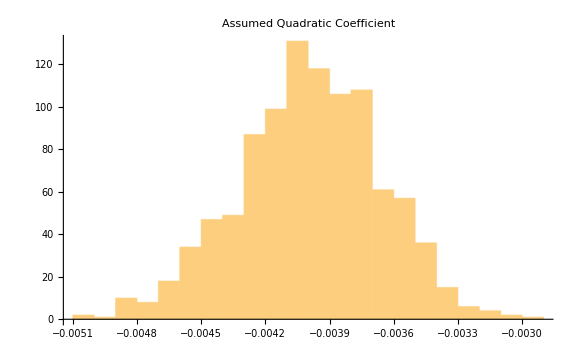

```mathematica
pl1=Histogram[ta2,PlotLabel->"Assumed Quadratic Coefficient",ImageSize->Large]
```

### Monte-Carlo of both the distribution and the quadratic term.

```mathematica
ta=RandomVariate[dist2,Length[f1]]
```

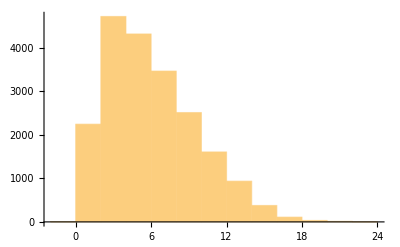

```mathematica
Histogram[ta]
```

```mathematica
ta2=Table[lm2=LinearModelFit[reg1[.75],{1,x,x^2},x];lm2[x][[3]][[1]],{z,1,10^3}]
```

{0.000511964,0.000188705,-0.000231808,-0.0000932095,0.000204079,0.000548984,-0.0000417178,-0.000274952,0.000299789,-0.000259416,-0.0000567765,0.000473266,-0.000141977,-0.000566188,0.000305066,0.000151646,0.000675753,0.000303268,0.000203871,0.000410536,0.000131856,0.000229207,-0.000465903,0.0000995657,0.000275773,0.000249919,0.0000860105,0.0000345663,0.000119635,0.000166463,-0.0000194701,0.000455509,0.00034492,0.000354767,0.000218247,-0.000725646,0.000606195,-0.000143791,0.00042354,-0.000481784,0.000424022,0.000231796,0.000195154,-0.000104637,-0.0000930933,0.000652471,-0.000566604,-0.000716179,-0.000233691,0.000443393,0.000230116,0.000449249,-0.000404005,0.000225691,0.0000658572,-0.000154041,0.00044444,0.000291561,0.000238813,-0.000534983,-0.000703539,0.000296102,-0.000543944,0.00031651,-0.000732159,0.0000364109,0.0000392544,-0.0000812077,0.000120376,-0.0000774643,-4.57916×10^-6,0.000261728,0.0000593072,-0.0000407136,-0.00040027,0.0000864453,0.000605457,0.0000238638,0.00014391,-0.0000780144,0.000558219,0.0000636572,0.0000633699,0.000131254,0.000377611,0.0000226903,-0.0000479981,0.00051433,-0.00018887,-0.000117344,-0.0000233347,0.000215627,-0.0000583097,-0.000120174,0.000212643,0.000182015,-0.0000361191,0.000282089,-0.00083808,0.000242606,0.0000767512,0.0000753906,-0.00022585,-0.000169544,-0.000307374,0.000199272,-2.44218×10^-6,-0.000303767,0.000652861,-0.0000981924,0.000264321,-0.0000954701,-0.0000473075,0.000209121,0.000338222,0.000202912,-0.000171945,-0.000256495,0.000139816,-0.0000359902,-0.000550596,-0.000617366,-0.000119209,-0.000129469,-0.0000727677,-0.0000420699,0.000478248,-0.000242541,-0.0000569077,0.0000358335,-0.000105216,-0.0000352199,0.000107253,0.000406483,-0.000168606,-0.0000190839,0.000503224,-0.000341778,0.000261696,-0.000167707,0.0000505867,-0.000185622,0.000538536,-0.000122865,-0.0000956508,-0.000266401,-0.000226,-0.000160109,-0.000381127,0.000483843,0.000527801,-0.0000227512,0.000333101,0.000181159,0.0000389423,0.000762753,-0.0000385871,-0.000322071,-0.000191156,0.000284923,0.000471323,0.000164413,-0.000197318,-0.000149897,-0.000519266,0.000101437,-0.000352519,0.00016281,3.77848×10^-6,0.000402862,-0.000285741,-0.000183835,0.0000624773,-0.0000872459,-0.000128808,-0.000411481,0.000125211,0.000223679,0.000217672,0.000457551,-0.000370361,0.0000838001,0.0000302841,-0.000313633,0.000144661,0.000339219,-0.0000485574,-0.000191897,-0.0000376246,0.000158418,0.000603162,0.000207277,-0.000105008,0.000532625,0.0000404739,-0.00030423,0.00054077,-0.000325969,0.0000713243,0.000462042,-0.000351474,0.000165073,0.000137345,0.000574585,6.10903×10^-7,-0.000126205,-0.000176026,-0.0000454331,-0.000242252,0.0000699326,0.000638726,0.0000971214,-0.000197451,0.0000314697,0.00027989,-0.0006634,0.0000635527,0.00058543,0.000487711,-0.000178871,1.9684×10^-6,-0.0000597328,-0.000142011,0.000242765,0.0000871923,0.000408758,0.0000756193,0.000249929,-0.000524532,0.000210144,-0.000856048,-0.000207865,0.000189893,0.0000683697,0.0000191394,0.000492104,0.0000552202,-0.0000254324,0.000234344,0.0000426802,-0.000543175,-0.000102635,-0.0000666617,-0.000132742,-0.0000609871,0.000255679,-0.000173161,0.000274647,0.000675966,-0.000405661,0.0000504141,-0.000321643,-0.000101356,0.0000696506,0.000593582,0.000504758,0.000207007,-0.000281758,-0.0000973518,0.0001924,-1.66081×10^-6,-0.000361297,0.00056722,0.000275876,-0.0000498064,0.000029673,0.000199801,-0.0000198098,0.000170737,0.000371177,0.000338496,0.000192015,-0.000442777,-0.000412979,0.000492828,0.000243133,-0.0000690319,0.000130007,-0.000884981,-0.000589843,-0.000531605,-0.000368422,-0.000408425,0.000535107,-0.000226412,0.000327086,-0.000234217,-0.0000210003,5.75739×10^-6,-0.0000225134,0.000169775,0.000191763,-0.000308394,-0.000389973,0.000278648,0.000116368,0.00035679,0.0000993246,0.000308455,0.000489235,9.21384×10^-6,-0.00038641,0.000306379,0.000109245,0.000152706,0.000437238,0.0000819799,-0.00036368,-0.0000726519,0.000381903,-0.000350599,-0.000284825,-0.000101678,0.000303342,0.000319003,0.000194546,-0.000310083,0.0000543462,0.000146026,0.000129871,-0.000065913,0.000118622,-0.000192973,0.000248257,0.0000661688,-0.000310741,0.000209306,0.000148689,-0.000181638,-0.000071399,-0.000110878,-0.000199147,0.00022493,-0.000342127,0.0005506,-0.000281483,-0.000150968,0.0000772727,-0.000326093,0.000270468,0.000470339,-0.000133809,-0.0001609,-0.000138513,-0.000173059,-0.0000277252,0.000066365,5.59445×10^-7,0.000121247,-0.0000404943,-0.000248882,0.0000871626,0.000253179,0.000374144,-0.0000194747,-0.000712302,-0.000201827,-0.0000354099,-0.000240324,0.000127653,-0.000372211,0.000508312,0.0000701246,-0.000119692,-0.000281513,-0.000256948,0.000325326,0.0000909699,-0.000104748,0.000352332,0.000474956,-0.00024519,0.0000499448,0.000669876,0.000202017,0.00040728,0.000253491,0.000182116,-0.0000209244,0.000258875,-0.000108395,0.000314705,0.000519937,0.000322714,0.000479191,6.74122×10^-6,0.000549571,-0.0000325406,0.000127602,-0.000542181,0.00014806,-0.000274518,-0.000731011,-0.0000537647,0.000170585,0.0000320095,0.000220938,0.000204836,0.000265496,0.00077615,0.000160668,0.000163142,0.000171777,-0.000200362,-0.0000874281,0.0000679443,0.000608831,-0.000269181,0.00018223,0.000490506,0.00037101,-0.000183005,0.000159914,-0.000135491,-0.0000766815,0.000167233,0.000584972,-0.000389415,-0.000172675,0.0000874928,-0.0000301484,0.000142482,0.0000313785,0.000202859,0.0000676247,0.000323592,-0.000260342,-0.0000370667,0.000303751,0.0000597867,-0.000110234,-0.000149479,0.000350502,0.000234225,0.000279897,-0.000133809,-0.000172107,-0.000131711,0.000436617,0.000702346,0.000456673,0.000105166,0.000304997,0.000402418,0.00032801,-0.0000559882,0.000305202,-0.00035476,-0.00039236,0.000100201,-0.000717106,0.00042467,-0.000100784,0.0000406423,-0.000178458,-0.0000178103,0.000656718,0.000167935,0.000592931,0.0000212274,0.000059769,0.000350082,0.000369915,-0.000382674,-0.000279494,0.000266763,0.000537553,-0.000308988,0.0000693545,0.000138057,-0.000449459,0.000123748,-0.000343288,0.00022631,-0.0000842639,-0.000135249,0.0000263089,-0.000259622,-0.000147666,0.000355545,-0.000195616,-0.000133679,-0.000276122,0.000240452,0.000114351,-0.000262267,-0.000293196,0.000119625,-1.01114×10^-6,0.000355055,0.000111444,-0.000124321,-0.000452247,-0.000094596,0.000335788,0.000404989,0.000151999,0.00011656,-0.000318107,-0.000365488,0.000418386,0.000232985,0.000389769,0.000372176,0.000468648,0.00030826,0.000482296,0.000244581,0.000264909,-0.000373183,-0.000161263,0.000118878,0.000156103,0.000289155,0.000184678,-0.0000208851,-0.000694304,0.000323069,0.000251736,0.0003784,-0.000890364,-0.0000390217,-0.000379154,-0.000193069,-0.0000385422,-8.22778×10^-6,0.00104851,-0.0000685022,-0.0000330993,-0.000236654,0.000349968,-0.000212567,-0.000148963,0.00015839,0.000592289,-0.000107604,-0.0000142935,0.000504998,-0.0000809733,-0.000588025,0.000364059,-0.000291179,0.0000354076,-0.000306224,0.000243546,-0.000160439,0.000258234,-0.0000654307,0.000089841,0.000309493,-0.000318889,-0.000295557,0.000440665,0.000356399,0.000352567,0.000291235,0.0000509643,0.000183375,-0.000105515,-0.000211903,-0.000455533,-0.0000981633,0.000151482,-0.000142405,0.0000389318,0.00045551,0.0000176317,-0.000587385,-0.000311888,-0.0000552853,-0.0000591431,-0.0000662355,0.000249645,0.000613736,0.000151959,0.000499835,0.000207047,-0.000247728,-0.000106987,-0.00027173,0.000118677,-0.000510575,-0.000121941,0.0000873022,0.000231054,0.0000829628,0.000231605,0.000318671,0.0000522161,-0.000125497,0.000121332,0.0000783361,0.000340113,0.0000204039,0.000366815,0.000180665,-0.0000782014,0.000397044,-0.000118055,-0.0000908576,-0.00043519,-0.0000643827,0.000307437,0.000179214,-0.000199814,-0.0000234863,-0.000223585,-0.0000104305,0.0000120268,-0.000237013,0.00011142,-0.000631323,0.000309995,0.000212955,0.0000738672,0.000318864,0.000355412,0.000909043,-0.000244605,0.000130018,0.000184591,0.000075703,-0.000116216,-0.000355468,0.00049522,0.000159831,-0.00037988,0.0000222179,0.000128097,-0.000367361,0.00034072,6.48054×10^-6,0.0000518358,0.000506536,-0.000353075,0.0000578739,0.000250115,0.000391724,0.0000522788,-0.0000163369,0.000413468,0.000215239,0.000354002,0.00022403,0.000238802,0.000137041,0.000101893,0.000550547,-0.0000716959,-0.000296854,-0.000186412,0.000553451,-0.0000130763,-0.000076474,-0.000104723,-0.000598329,0.000188129,0.000250374,-0.000187679,-0.000204729,0.000637694,-0.000547643,-0.000518148,-0.000144883,0.000150754,0.00045329,-0.000296403,-0.00048957,-0.000583979,0.000174241,0.000126336,-4.03685×10^-7,-0.000177567,-0.000639392,-0.000260966,0.000590631,-0.000581296,-0.000351022,1.84144×10^-6,-0.000191314,-0.000324367,0.000703408,0.000979221,-0.000214649,0.000124506,0.000151885,-0.000168787,-0.000091121,-0.0000954371,0.000406937,0.000114191,-0.000372797,0.000195406,0.000430975,0.0000966249,0.000141934,0.00010665,-0.000317635,0.000280266,-0.000418053,-0.0000321533,0.00034306,-0.000160835,0.000123316,-0.00017555,0.000386414,-0.000571635,-0.0000119193,0.0000319099,0.000411713,-0.0000909458,-0.0000333561,0.000553594,0.000226144,0.000615576,-0.00040644,0.000531379,0.000193042,0.000160132,0.0000431694,-0.000148001,-0.0000413065,0.000222295,0.000125917,0.000959214,-0.000318461,0.0000634164,-0.000426894,-0.00045978,0.000599905,0.000310254,0.00057736,-0.0000734577,-0.000128054,-0.000566334,0.000358442,0.0000657341,0.000753326,0.000536162,0.000646273,-0.000124596,-0.000203647,0.0000602039,0.000345816,-0.000111239,0.000304091,0.000192353,-5.84034×10^-6,0.000825446,-0.000115582,0.000371774,0.000250596,-0.000377285,-0.000655686,0.000190536,0.0000779927,-0.000361143,-0.000169929,0.000864207,0.0000428856,-0.000110271,0.000290982,0.000147376,0.000545655,-0.000557436,-0.000266814,0.000233699,-0.000372738,-0.000341393,-0.000362716,-0.000399583,-0.000146947,-0.000775274,-0.000355953,-0.000153515,-0.0000132552,0.0000504605,0.000243405,-0.0000209471,0.000481984,0.0000629717,-0.000662157,0.0000358575,0.000358717,-0.0000563568,0.000163427,-0.0000259302,-0.000141147,9.09819×10^-6,0.000031781,0.000362361,-0.00068776,-0.000303415,0.000101615,-0.000414879,0.000211408,0.0000335751,-0.000135903,-0.0000610954,-0.000166954,-0.000142219,0.000707541,0.000195049,-0.000039566,0.000540371,-0.000208306,-0.000240088,-0.000172607,0.00054115,-0.000332864,0.000430422,0.000481055,-0.000377843,0.000331404,0.0000870443,0.0000956982,-0.000281149,0.000623659,0.000274526,-0.000314139,0.00030716,0.00017854,0.000403536,0.000133904,0.000231503,0.0000236537,-0.000344906,0.000357384,0.000161369,0.000341082,-0.000179675,0.0000369093,0.000101607,0.000160018,0.000618046,-0.0000938223,0.0000818032,-0.000242517,0.000515351,0.000368403,-0.000244957,0.0000514589,-0.000065304,-0.000101103,-0.0000238755,-0.000437054,-0.000481573,0.000342696,0.000526466,0.000894557,0.000665357,-0.0000384403,0.000121741,0.000447756,0.000112364,-0.000176591,-0.0000103316,-0.000115099,0.000244495,0.000480304,0.000242053,0.000323892,-0.000471268,-0.00012729,0.0000527707,0.000384249,-0.000121862,0.000491338,0.000535416,0.000199833,0.000246499,0.000333701,-0.000219512,0.0000116292,0.000169846,-0.000460043,0.00021096,-0.000222821,-0.000140355,-0.000218755,0.000210268,0.000681386,0.000151446,-0.000172257,0.0000665452,0.000213469,-0.000329806,0.000360113,-0.000194702,-0.000140068,-0.000128096,0.00022555,0.000333674,-0.0000351128,-0.00057859,0.000379855,0.000400674,-0.000339305,0.000441224,-0.000191319,-0.000196393,0.000100463,0.000323749,0.000742529,-0.00032371,-0.0000281045,0.000203456,0.0000675788,0.000455306,-0.000113571,0.000216778,0.0000293324,0.000791817,0.000309167,-0.0000755222,-0.0000644277,-0.0000432091,0.000125651,-0.000217222,0.0000861671,-0.000116178,-0.000067006,-0.0000988976,1.78663×10^-6,-0.000232578,0.000209092,1.64607×10^-6,0.000229118,0.000273987,0.000245504,0.000138508,0.000335076,-0.000104544,0.000427984,-0.000143811,0.000160811,-0.00025918,0.000663081,-0.000329537,0.000498215,0.000328716,0.000925286,0.0000855833,0.000195739,0.000477573,-0.000253614,-0.0000625849,0.00013636,0.000214768,-0.0000882811,0.000329933,-0.000457085,0.000576133,-0.0000735221,-0.000135209,-0.000284135,0.00030653,-0.000570238,-0.000475945,-0.000433754,0.000433123,-0.00021309,-0.000250078,0.000583707,0.000113214,-0.0000205793,0.000182254,-0.0000318644,0.000134236,-0.00053848,-0.000446819,-0.000225895,0.0000311465,-0.000218642,0.000134574,-0.0000229864,-0.000496228,-0.0000275258,0.000123174,-0.0000395042,0.000326348,0.000239504,0.0000352462,0.000561726,-0.000215423,0.000444339,0.000345841,0.000296911,-0.000459143,-0.0000489265,0.000377992,0.000280643,0.000165966,-0.00011572,-0.000447798,0.000516181,-0.000191942,0.0000223415,0.000353257,0.000447476}

```mathematica
{Mean[ta2],StandardDeviation[ta2],Kurtosis[ta2]}
```

{0.0000509245,0.000316548,2.95389}

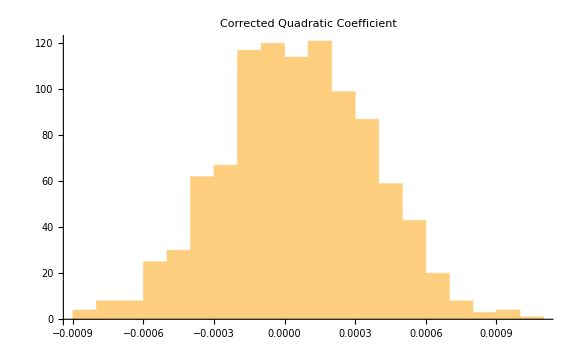

```mathematica
pl2=Histogram[ta2,PlotLabel->"Corrected Quadratic Coefficient",ImageSize->Large]
```

### Examining R^2

Do we need to define n?

```mathematica
Mean[FRatioDistribution[n,n]]
```

Piecewise[{{n/(-2+n), n>2}, {Indeterminate, True}}]

Why did this transformation fail?

```mathematica
EstimatedDistribution[ta2,FRatioDistribution[n,n]];
```

EstimatedDistribution::ntsprt: One or more data points are not in support of the process or distribution FRatioDistribution[n,n].

```mathematica
TransformedDistribution[x/y,{x\[Distributed]ChiSquareDistribution[n],y\[Distributed]ChiSquareDistribution[n]}]
```

FRatioDistribution[n,n]

```mathematica
LinearModelFit[reg1[.75],{1,x,x^2},x]["RSquared"];
```

Verify the ta3 is legitimate.

```mathematica
ta3=Table[lm2=LinearModelFit[reg1[.88],{1,x,x^2},x]["RSquared"],{z,1,10^3}];
```

```mathematica
{Mean[ta3],StandardDeviation[ta3],Kurtosis[ta3]}
```

{0.0000964338,0.0000960211,9.03847}

Plot the last histogram which shows that it is all in the left.

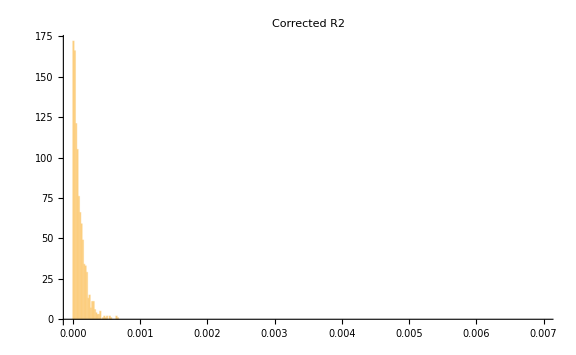

```mathematica
pl3=Histogram[ta3,PlotLabel->"Corrected R2",PlotRange->{{0,0.007},Automatic},ImageSize->Large]
```

Plot the comparisons between the various grids.

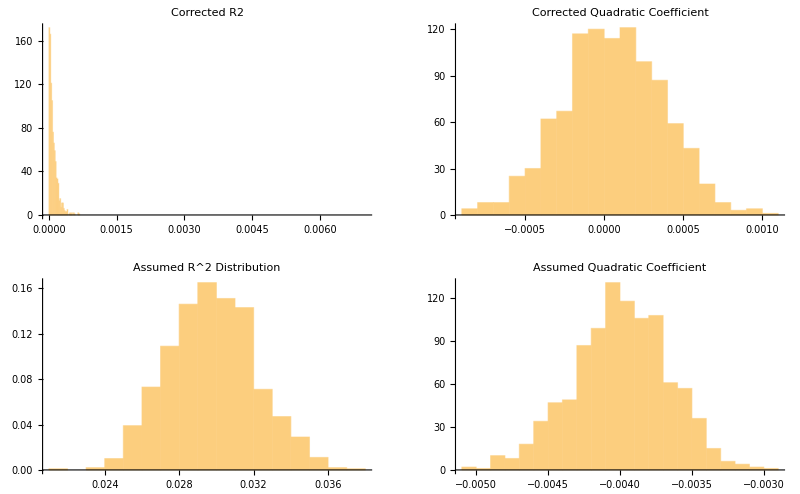

```mathematica
GraphicsGrid[{{pl3,pl2},{pl0,pl1}}]
```